```mathematica
NBodySimulation["InverseSquare",{
<|"Mass"->1,"Position"->{1,0},"Velocity"->{1,0}|>,
<|"Mass"->1,"Position"->{-1,0},"Velocity"->{0,-1}|>
},10]
```

NBodySimulationData[…]

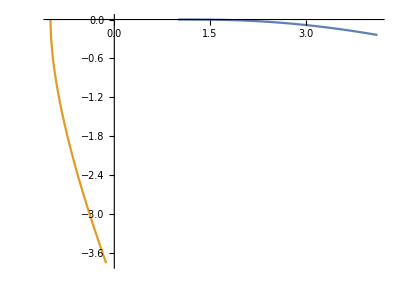

```mathematica
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->1,"Position"->{1,0},"Velocity"->{1,0}|>,
<|"Mass"->1,"Position"->{-1,0},"Velocity"->{0,-1}|>
},10][All,"Position",t]]
,{t,0,4}]
```

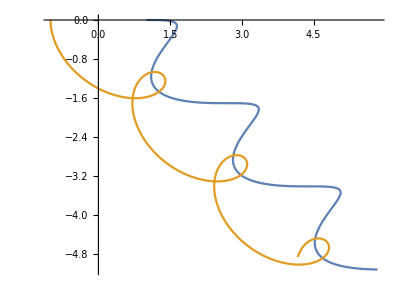

```mathematica
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{1,0}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>
},10][All,"Position",t]]
,{t,0,10}]
```

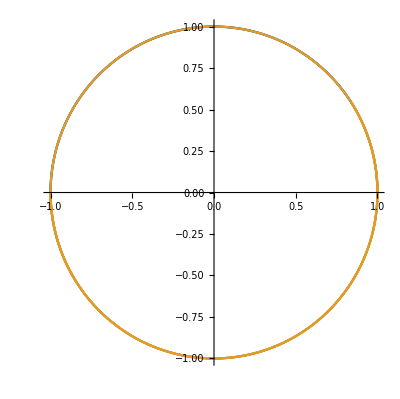

```mathematica
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{0,1}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>
},10][All,"Position",t]]
,{t,0,10}]
```

```mathematica
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{0,-1}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>
},10][All,"Position",t]]
,{t,0,10}]
```

NDSolve`Iterate::ndsz: At t == 1.11072, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{0,1}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>
},10][All,"Position",t]]
,{t,0,10}]
```

-Graphics-

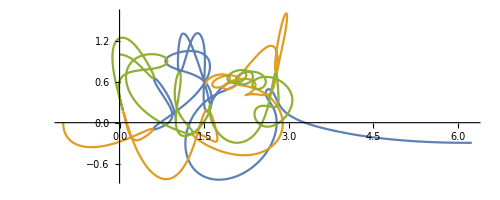

```mathematica
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{0,1}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->4,"Position"->{0,1},"Velocity"->{1,0}|>
},10][All,"Position",t]]
,{t,0,10}]
```

```mathematica
With[{limit=10},
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{0,1}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->4,"Position"->{0,1},"Velocity"->{1,0}|>
},limit][All,"Position",t]]
,{t,0,a}]
,{a,0.01,limit}]
]
```

```mathematica
With[{limit=10},
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->4,"Position"->{1,0},"Velocity"->{0,1}|>,
<|"Mass"->4,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->4,"Position"->{0,1},"Velocity"->{-1,0}|>
},limit][All,"Position",t]]
,{t,0,a}]
,{a,0.01,limit}]
]
```

```mathematica
x^2
```

x^2

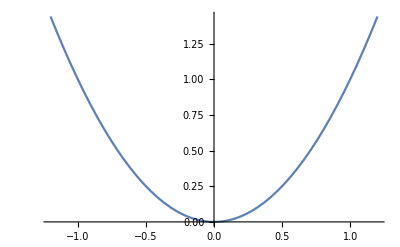

```mathematica
Plot[x^2,{x,-1.2,1.2}]
```

```mathematica
Solve[D[x^2,x]-g[x]==0,g[x],Reals]
```

{{g[x]→2 x}}

```mathematica
Sign[x^2]==1
```

Sign[x]^2==1

```mathematica
Reduce[Sign[x]^2==1]
```

Sign[x]==-1||Sign[x]==1

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
x-x^3/6+x^5/120-x^7/5040+x^9/362880
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

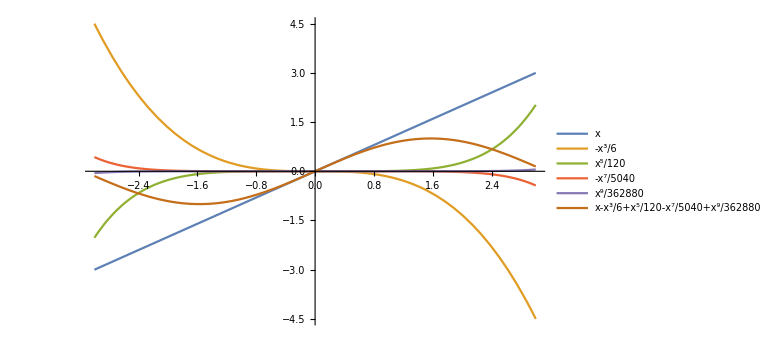

```mathematica
Plot[
{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-3,3}
,PlotRange->Full,PlotLegends->"Expressions",ImageSize->Large]
```

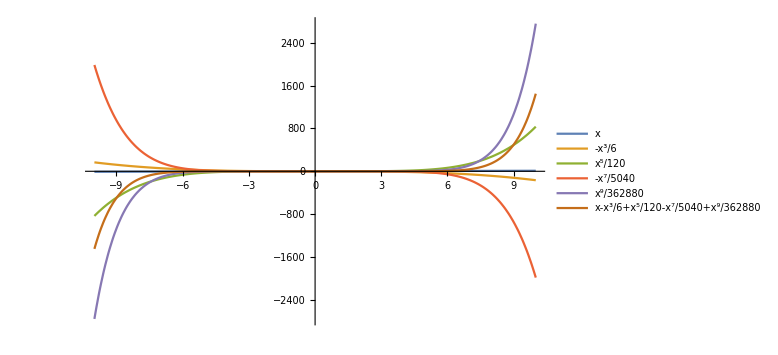

```mathematica
Plot[
{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotRange->Full,PlotLegends->"Expressions",ImageSize->Large]
```

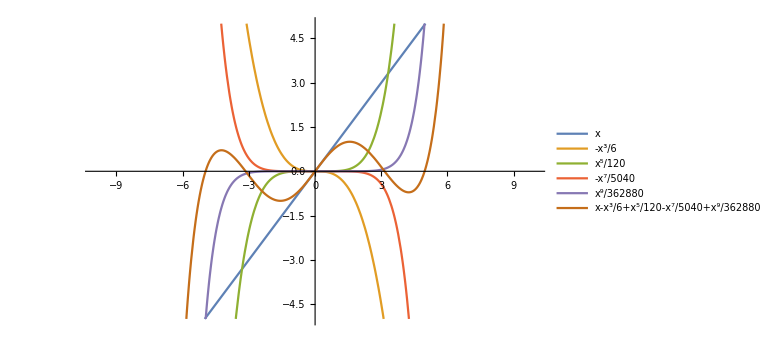

```mathematica
Plot[
{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotRange->{{-10,10},{-5,5}},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
FullSimplify[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}/(Total@{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}),x∈Reals]
```

{362880/(362880-60480 x^2+3024 x^4-72 x^6+x^8),-(60480 x^2)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),(3024 x^4)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),-(72 x^6)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),x^8/(362880-60480 x^2+3024 x^4-72 x^6+x^8)}

```mathematica
{362880/(362880-60480 x^2+3024 x^4-72 x^6+x^8),-(60480 x^2)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),(3024 x^4)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),-(72 x^6)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),x^8/(362880-60480 x^2+3024 x^4-72 x^6+x^8)}
```

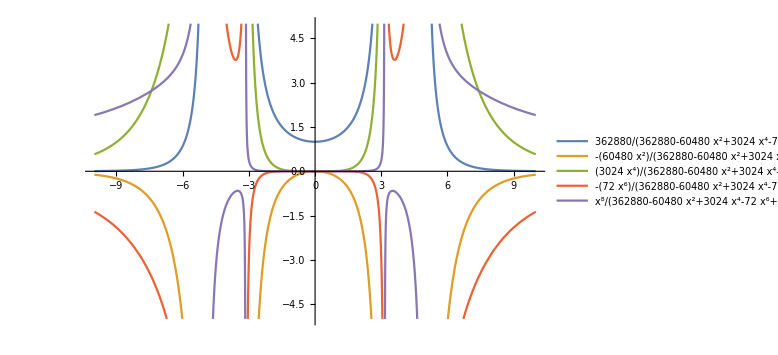

```mathematica
Plot[
{362880/(362880-60480 x^2+3024 x^4-72 x^6+x^8),-(60480 x^2)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),(3024 x^4)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),-(72 x^6)/(362880-60480 x^2+3024 x^4-72 x^6+x^8),x^8/(362880-60480 x^2+3024 x^4-72 x^6+x^8)}
,{x,-10,10}
,PlotRange->{{-10,10},{-5,5}},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
FullSimplify[(Abs@{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880})/(Total@Abs@{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}),x∈Reals]
```

{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}

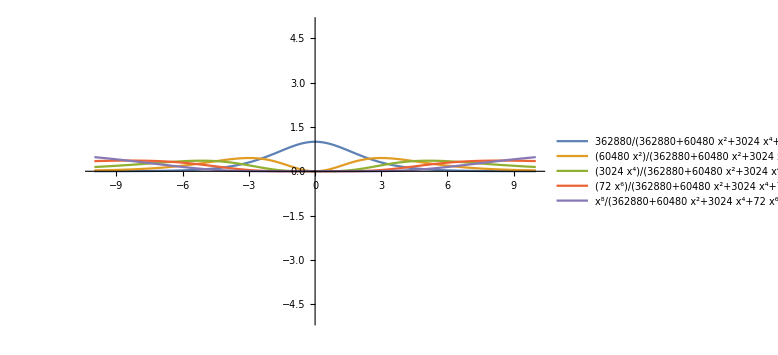

```mathematica
Plot[
{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}
,{x,-10,10}
,PlotRange->{{-10,10},{-5,5}},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
ArcCurvature[{x,f[x]+g[x]},x]==ArcCurvature[{x,g[x]},x]+ArcCurvature[{x,f[x]},x]
```

√((f''[x]+g''[x])^2/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^3))==√(f''[x]^2/((1+f'[x]^2)^3))+√(g''[x]^2/((1+g'[x]^2)^3))

```mathematica
DSolve[%25,{f[x],g[x],f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[√((f''[x]+g''[x])^2/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^3))==√(f''[x]^2/((1+f'[x]^2)^3))+√(g''[x]^2/((1+g'[x]^2)^3)),{f[x],g[x],f[x],g[x]},{x}]

```mathematica
DSolve[√((f''[x]+g''[x])^2/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^3))==√(f''[x]^2/((1+f'[x]^2)^3))+√(g''[x]^2/((1+g'[x]^2)^3)),{f[x]},{x}]
```

$Aborted

```mathematica
Binomial[k+1,k]
```

1+k

```mathematica
Binomial[k+1,2]
```

1/2 k (1+k)

```mathematica
Binomial[k+1,1]
```

1+k

```mathematica
Binomial[4,6]
```

0